# Riemannian metrics and variants

In this notebook, we briefly illustrate the use of the HamiltonFastMarchingLibrary to compute distances and geodesic paths w.r.t Riemann metrics and two Finslerian variants, known as Randers metrics and asymmetric quadratic metrics.

The Riemannian and asymmetric quadraic models are implemented in dimension 2 and 3, but only the two dimensional ones are illustrated here.

A much more expansive documentation, with use case examples, is available in the Python Language, see https://github.com/Mirebeau/AdaptiveGridDiscretizations

## Utility functions

Display

```mathematica
GraphicsHFM[hfmIn_,hfmOut_]:=Module[{
values="values"/.hfmOut,
geodesics="geodesics"/.hfmOut,
dataRange={0,#}&/@(("gridScale"/.hfmIn) *( "dims"/.hfmIn) )
(* assuming "origin" is not specified*)
},
ListContourPlot[Transpose[values],DataRange->dataRange,Epilog->Line/@geodesics,AspectRatio->Automatic]
];
```

```mathematica
(*SetDirectory["/Users/mirebeau/Dropbox/Programmes/Github/HamiltonFastMarching/Interfaces/MathematicaHFM/ExampleFiles/FileBased/tmp"] (*Debug*)*)
```

## Riemannian metrics

Constant metric

Field verbosity defaults to 1
Field origin defaults to {0,0}
Field order defaults to 1
Field seedRadius defaults to 0
Fast marching solver completed in 0.004565 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.001
Field geodesicVolumeBound defaults to 8.45

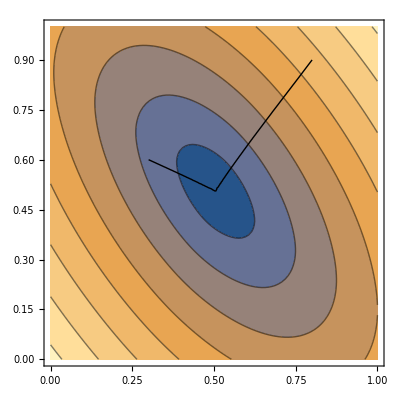

```mathematica
Module[{n=100,hfmIn,hfmOut},
hfmIn = {
"dims"->{n,n},
"gridScale"->1./n,
"seeds"->{{0.5,0.5}},
"metric"->{1,0.5,0.7}, (*Metric components xx,xy,yy*)
"exportValues"->1,
"tips"->{{0.8,0.9},{0.3,0.6}}
};

hfmOut = RunExec["FileHFM_Riemann2",hfmIn];
Print["log"/.hfmOut];
GraphicsHFM[hfmIn,hfmOut]
]
```

Varying metric

Metric dimensions : {nx,ny,ncomp} = {100,150,3}

Field verbosity defaults to 1
Field origin defaults to {0,0}
Field order defaults to 1
Field seedRadius defaults to 0
Fast marching solver completed in 0.005563 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.001
Field geodesicVolumeBound defaults to 8.45

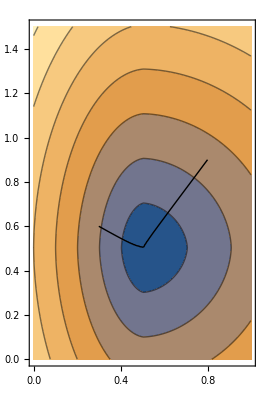

```mathematica
Module[{nx=100,ny=150,h=1/100,hfmIn,hfmOut},
hfmIn={"dims"->{nx,ny},
"gridScale"->h,
"seeds"->{{0.5,0.5}},

(*Convention: row major, with points at cell centers*)
"metric"->Table[
With[{x=(ix-0.5)*h,y=(iy-0.5)*h},
If[x>0.5,{1,0.,1},{4,0,1}]],
{ix,1,nx},{iy,1,ny}],

"exportValues"->1,
"tips"->{{0.8,0.9},{0.3,0.6}}
};
Print["Metric dimensions : {nx,ny,ncomp} = ",Dimensions["metric"/.hfmIn]];
hfmOut = RunExec["FileHFM_Riemann2",hfmIn];
Print["log"/.hfmOut];
GraphicsHFM[hfmIn,hfmOut]
]
```

## Randers metrics

Constant metric

Field verbosity defaults to 1
Field arrayOrdering defaults to RowMajor
Field origin defaults to {0,0}
Field cosAngleMin defaults to 0.5
Field refineStencilAtWallBoundary defaults to 0
Field order defaults to 1
Field seedRadius defaults to 0
Fast marching solver completed in 0.01083 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.001
Field geodesicVolumeBound defaults to 8.45

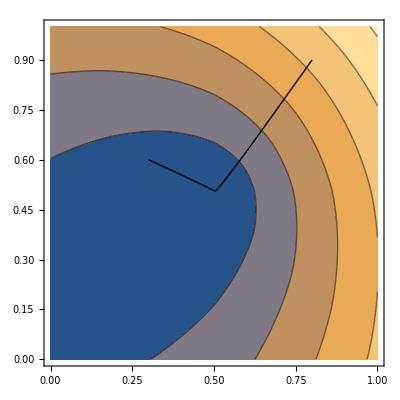

```mathematica
Module[{n=100,hfmIn,hfmOut},
hfmIn = {
"dims"->{n,n},
"gridScale"->1./n,
"seeds"->{{0.5,0.5}},
"metric"->{1,0.,1.,0.7,0.4}, (*Metric components mxx,mxy,myy,  vx,vy*)
"exportValues"->1,
"tips"->{{0.8,0.9},{0.3,0.6}}
};

hfmOut = RunExec["FileHFM_Rander2",hfmIn];
Print["log"/.hfmOut];
GraphicsHFM[hfmIn,hfmOut]
]
```

## AsymmetricQuadratic metrics

Constant metric

Field verbosity defaults to 1
Field arrayOrdering defaults to RowMajor
Field origin defaults to {0,0}
Field cosAngleMin defaults to 0.5
Field refineStencilAtWallBoundary defaults to 0
Field order defaults to 1
Field seedRadius defaults to 0
Fast marching solver completed in 0.00845 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.001
Field geodesicVolumeBound defaults to 8.45

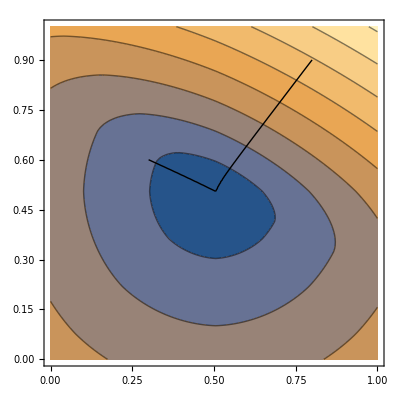

```mathematica
Module[{n=100,hfmIn,hfmOut},
hfmIn = {
"dims"->{n,n},
"gridScale"->1./n,
"seeds"->{{0.5,0.5}},
"metric"->{1,0.,1.,1.,2.}, (*Metric components mxx,mxy,myy,  vx,vy*)
"exportValues"->1,
"tips"->{{0.8,0.9},{0.3,0.6}}
};

hfmOut = RunExec["FileHFM_AsymmetricQuadratic2",hfmIn];
Print["log"/.hfmOut];
GraphicsHFM[hfmIn,hfmOut]
]
```